# scale free network and power law

```mathematica
ba3=RandomGraph[BarabasiAlbertGraphDistribution[10^5,3]];
```

```mathematica
empddistrBA3=EmpiricalDistribution[VertexDegree[ba3]]
```

DataDistribution[…]

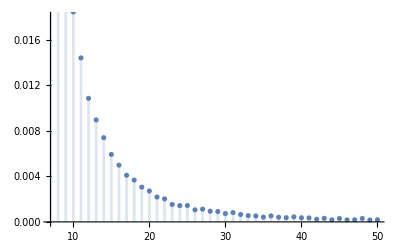

```mathematica
DiscretePlot[PDF[empddistrBA3,k],{k,7,50}]
```

```mathematica
Take[Table[PDF[empddistrBA3,k],{k,7,50}],10]
{4737/100000,1659/50000,2419/100000,1897/100000,697/50000,253/25000,223/25000,363/50000,18/3125,499/100000}
```

{37/800,3301/100000,19/800,921/50000,1439/100000,271/25000,179/20000,739/100000,37/6250,249/50000}

{4737/100000,1659/50000,2419/100000,1897/100000,697/50000,253/25000,223/25000,363/50000,18/3125,499/100000}

```mathematica
loglogba3=Table[{Log[PDF[empddistrBA3,k]],Log[k]},{k,7,50}];
```

```mathematica
a=Take[loglogba3,10]
{{-Log[100000/4737],Log[7]},{-Log[50000/1659],Log[8]},{-Log[100000/2419],Log[9]},{-Log[100000/1897],Log[10]},{-Log[50000/697],Log[11]},{-Log[25000/253],Log[12]},{-Log[25000/223],Log[13]},{-Log[50000/363],Log[14]},{-Log[3125/18],Log[15]},{-Log[100000/499],Log[16]}}
```

{{-Log[800/37],Log[7]},{-Log[100000/3301],Log[8]},{-Log[800/19],Log[9]},{-Log[50000/921],Log[10]},{-Log[100000/1439],Log[11]},{-Log[25000/271],Log[12]},{-Log[20000/179],Log[13]},{-Log[100000/739],Log[14]},{-Log[6250/37],Log[15]},{-Log[50000/249],Log[16]}}

{{-Log[100000/4737],Log[7]},{-Log[50000/1659],Log[8]},{-Log[100000/2419],Log[9]},{-Log[100000/1897],Log[10]},{-Log[50000/697],Log[11]},{-Log[25000/253],Log[12]},{-Log[25000/223],Log[13]},{-Log[50000/363],Log[14]},{-Log[3125/18],Log[15]},{-Log[100000/499],Log[16]}}

```mathematica
line=Fit[loglogba3,{1,x},x]
```

0.929112-0.345376 x

```mathematica
parabola=Fit[loglogba3,{1,x,x^2},x]
```

0.702009-0.424623 x-0.00643417 x^2

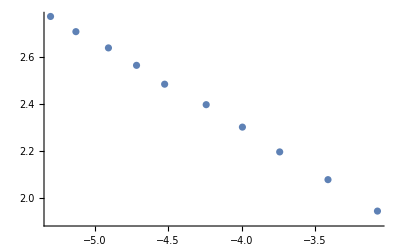

```mathematica
g1=ListPlot[a]
```

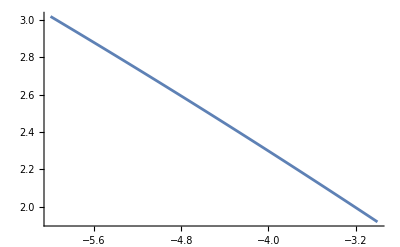

```mathematica
g2=Plot[parabola,{x,-6,-3}]
```

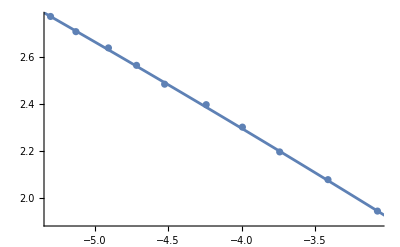

```mathematica
Show[g1,g2]
```

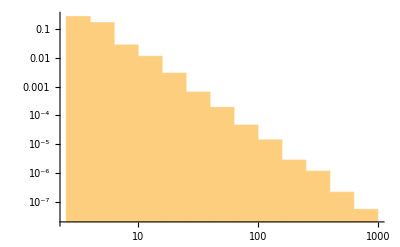

```mathematica
Histogram[VertexDegree[ba3],{"Log",10},{"Log","PDF"}]
```

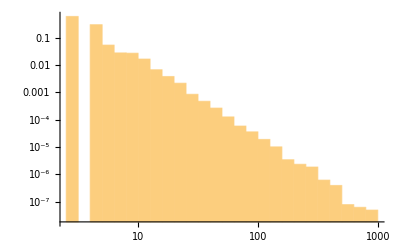

```mathematica
Histogram[VertexDegree[ba3],{"Log",25},{"Log","PDF"}]
```

```mathematica
g=ExampleData[{"NetworkGraph","Internet"}];
```

```mathematica
VertexCount[g]
```

22963

```mathematica
Round[EdgeCount[g]/VertexCount[g]]
```

2

```mathematica
baInternet=BarabasiAlbertGraphDistribution[VertexCount[g],Round[EdgeCount[g]/VertexCount[g]]]
```

BarabasiAlbertGraphDistribution[22963,2]

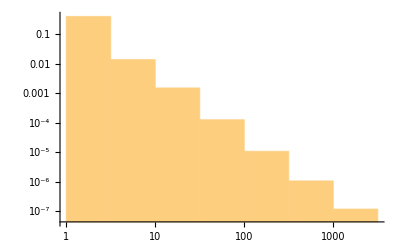
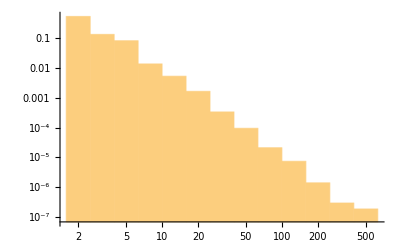

```mathematica
{Histogram[VertexDegree[g],{"Log",10},{"Log","PDF"}],Histogram[VertexDegree[RandomGraph[baInternet]],{"Log",10},{"Log","PDF"}]}
```

```mathematica
N[GlobalClusteringCoefficient[g]]
```

0.0111464

```mathematica
N[GlobalClusteringCoefficient[RandomGraph[baInternet]]]
```

0.000824565

```mathematica
ba2=RandomGraph[BarabasiAlbertGraphDistribution[10^5,2]];
empddistrBA2=EmpiricalDistribution[VertexDegree[ba2]]
```

DataDistribution[…]

```mathematica
ba4=RandomGraph[BarabasiAlbertGraphDistribution[10^5,4]];
empddistrBA4=EmpiricalDistribution[VertexDegree[ba4]]
```

DataDistribution[…]